Asumo que capturo varios períodos (>>10), de una señal periódica (o casi). Le hago la DFT, y sumo un intervalo de 9 puntos alrededor de los máximos locales, que chequeo, tengan frecuencias aproximadamente múltiplas, con cierta tolerancia.
No asumo que las muestras vienen equiespaciadas. Las transformo en uniformes con interpolación de orden 3. Remuestreo con el doble de puntos que la original.

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
data=SemanticImport["Clase G par doble +15-15-0.5vin-4ohm.txt"][All, Values]//Normal;
```

```mathematica
ts=TimeSeries[data, ResamplingMethod->{"Interpolation",InterpolationOrder->0}]
```

TimeSeries[…]

```mathematica
resample[ts_]:=ts[ts["FirstTime"] +(ts["LastTime"]-ts["FirstTime"])Range[0, 2 ts["PathLength"]]/(2 ts["PathLength"])];
```

```mathematica
halfLenght[l_List]:=l~Take~Ceiling[Length@l/2];
```

```mathematica
fftpot[ts_TemporalData]:=Abs[Fourier[resample[ts]]]^2//halfLenght;
```

```mathematica
potHarm[n_,Null,neig_:9][fftpot_]:=potHarm[n, First@Ordering[fftpot, -1]-1, neig];
potHarm[n_, fftstep_, neig_:9][fftpot_]:=Total[Take[fftpot,1+n fftstep+Round[{-1, 1} (neig-1)/2]]]
```

Luego, la distorsión

```mathematica
distortion[ts_TemporalData]:=With[{fpot=fftpot[ts]},
With[{fftstep=First@Ordering[fpot, -1]-1},

Table[potHarm[n,fftstep, 9][fpot], {n, 1, Min[50,Floor[ Length[fpot]/fftstep]]}]/.{fund_,harms___}:>√(Total[{harms}]/fund)

]]~UnitConvert~"Percent"
```

```mathematica
imp[fname_String]:=SemanticImport[fname][All, Values]//Normal//TimeSeries[#, ResamplingMethod->{"Interpolation",InterpolationOrder->3}]&;
```

```mathematica
ts=imp["test.txt"];
```

```mathematica
ta[-1, "data"]//distortion
```

0.488382 %

```mathematica
ListLinePlot[ta[1, "data"]~TimeSeriesWindow~{0.05, 0.053}]
```

```mathematica
FileNames["*.txt"]
```

{1kHz-vout-barrido-amplitud.txt,Clase G par doble +15-15-0.5vin-4ohm.txt,Clase G par doble +15-15-0.5vin-sin-carga.txt,Clase G par doble +15-15-resp-frec.txt,Clase G par doble +15-15-vout.txt}

```mathematica
ts2=SemanticImport["Clase G par doble +15-15-vout.txt"][All, Values]//Normal/*TimeSeries;
```

```mathematica
distortion[ts2]
```

0.469919 %

```mathematica
ts2
```

## Ancho de banda de potencia

Busco un umbral de distorsión, y barro, para distintas frecuencias, la amplitud a partir de la cual distorsiona. O sea, todo surge de un barrido en amplitud y en frecuencia. Si tengo 50 frecs y 50 amplitudes, hay 2500 barridos, y si cada uno tiene 50k muestras, es total 12.5 millones de muestras. Es manejable. Packed, son 100 megas.

```mathematica
t=Import["1kHz-vout-barrido-amplitud.txt", "String"];
```

```mathematica
ta=StringSplit[t, "Step Information: "]//Rest//Map[StringSplit[#, EndOfLine, 2]/.{h_, d_}:><|"A"->First@StringReplace[h,StartOfString~~ "A="~~m:NumberString~~c_~~___~~EndOfString:>(c/.{" ":>ToExpression[m],_:> ToExpression[m](c/."m"->0.001)})], "data"->TimeSeries[Normal@SemanticImportString[d]],ResamplingMethod->{"Interpolation",InterpolationOrder->3}|>&]//Dataset;
```

```mathematica
taD=ta[All, Append[#, "THD"->distortion[#["data"]]]&];
```

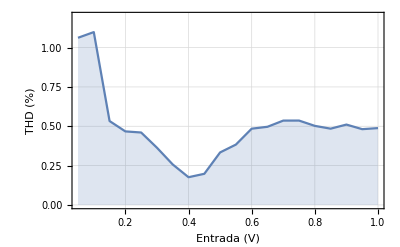

```mathematica
taD[ListLinePlot[#, PlotRange->{Full,{0, 1.2}}, PlotTheme->"Detailed", Filling->Axis,PlotRangePadding->0, FrameLabel->{"Entrada (V)", "THD (%)"}]&, {"A","THD"}]
```

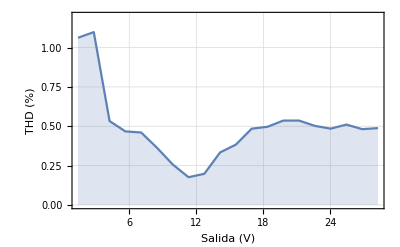

```mathematica
taD[ListLinePlot[#, PlotRange->{Full,{0, 1.2}}, PlotTheme->"Detailed", Filling->Axis,PlotRangePadding->0, FrameLabel->{"Salida (V)", "THD (%)"}]&, {#["A"]28.25&,"THD"}]
```

```mathematica
SemanticImport["test.txt"][Length]
```

13418

```mathematica
100000
```

```mathematica
1/100000
```

1/100000

```mathematica
√100000//N
```

316.228

```mathematica
(1/10000)^2
```

1/100000000

```mathematica
√2//N
```

1.41421